```mathematica
Clear[H];H[l_,t_]:=Sqrt[2 l +1]/2*(LegendreP[l,t] UnitStep[t+1] UnitStep[-t]+Cos[t] LegendreP[l,Sin[t]] UnitStep[t] UnitStep[π/2-t])
```

```mathematica
Clear[plots];Do[plots[i]=Plot[H[i,t],{t,-1,π/2}],{i,0,6}]
```

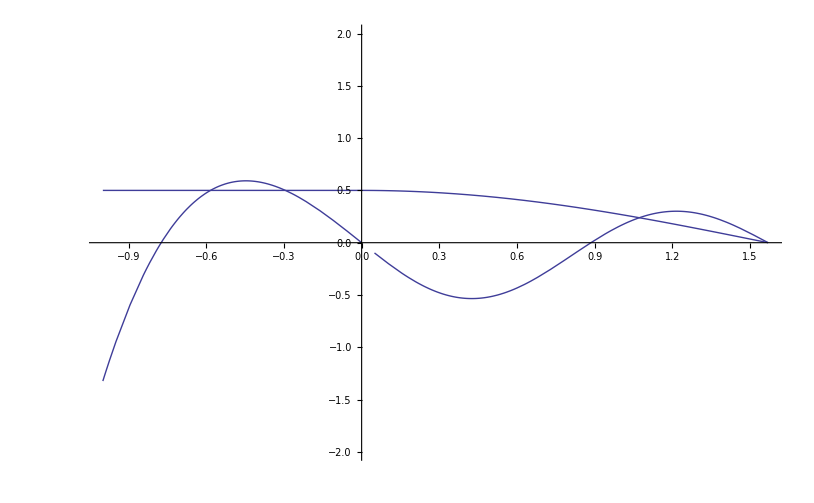

```mathematica
Show[plots[0],plots[3],PlotRange->{-2,2}]
```

```mathematica
LegendreP[3,-.8]
```

-0.08

```mathematica
order =6;
pp[t_]:=If[t==0,0,1]
Clear[H2];H2[l_,t_]:=Sqrt[2 l +1]/2*(LegendreP[l,t] UnitStep[t+1] UnitStep[-t] pp[t]+Cos[t] LegendreP[l,Sin[t]] UnitStep[t] UnitStep[π/2-t])
dt=0.0001;
t0 = -1;
tmax = 40;
NN=Round[(tmax-t0)/dt]
Do[
nom = "/home/toni.mateos/acustica/phds/phd_david/delayHRTF_analytic/isItMinimumPhase/h" <> ToString[l] <> ".txt";
Export[nom, Table[N[H2[l,t0+n dt]],{n,0,NN}]];
,{l,0,order}]
```

410000